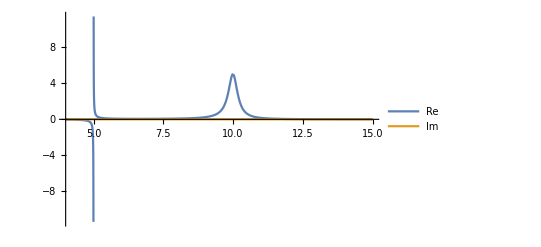

```mathematica
ClearAll;
e0=4.;
k0=1.;
Subscript[σ, k]=e0+k0+I 0.0;
Subscript[σ, n]=10.+0.2 I;
rkernel[E_,s1_,s2_,s3_]:=Re[1/((E-s1) (E-s2) (E-s3))]
ikernel[E_,s1_,s2_,s3_]:=Im[1/((E-s1) (E-s2) (E-s3))]
Plot[{rkernel[ee,Subscript[σ, k],Subscript[σ, n],Conjugate[Subscript[σ, n]]],ikernel[ee,Subscript[σ, k],Subscript[σ, n],Conjugate[Subscript[σ, n]]]},{ee,e0,15},PlotLegends->{"Re","Im"},PlotRange->Full]
```

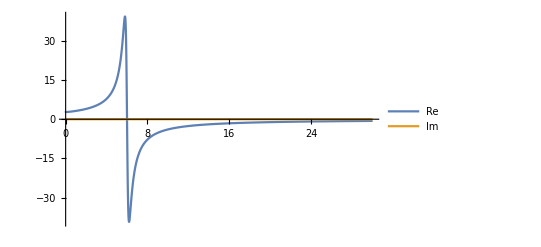

```mathematica
upperbnd=Infinity;
reP[kk_]:=NIntegrate[rkernel[ee,e0+kk,10.+0.2 I,10.-0.2 I],{ee,e0,e0+kk,upperbnd},Method->"PrincipalValue"]
imP[kk_]:=NIntegrate[ikernel[ee,e0+kk,10.+0.2 I,10.-0.2 I],{ee,e0,e0+kk,upperbnd},Method->"PrincipalValue"]
Plot[{reP[k],imP[k]},{k,0,30},PlotLegends->{"Re","Im"},PlotRange->Full]
```

```mathematica
NIntegrate[rkernel[ee,e0+kk,10.+0.2 I,10.-0.2 I],{ee,e0,upperbnd}]/.kk->1
```

1.6719

```mathematica
NIntegrate[rkernel[ee,e0+kk,10.+0.2 I,10.-0.2 I],{ee,e0,upperbnd,e0+kk},Method->{"PrincipalValue",Method->methodspec,"SingularPointIntegrationRadius"->ϵ}]./kk->1
```

```mathematica
Apart[1/((x-a) (x-b) (x-c))]
```

1/((a-b) (a-c) (-a+x))-1/((a-b) (b-c) (-b+x))-1/((a-c) (-b+c) (-c+x))

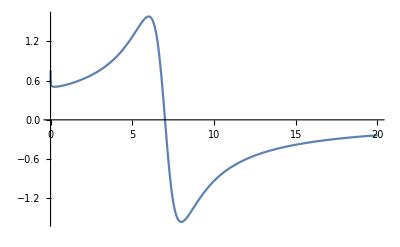

```mathematica
b=9;
c=11+I;
d=11-I;
Plot[NIntegrate[1/((x-(e0+kk)) (x-c) (x-d)),{x,e0,e0+kk,Infinity},Method->"PrincipalValue"],{kk,0,20},PlotRange->Full]
```